## 1.

### a.

```mathematica
DSolve[c'[t]==F/V cin-F/V c[t],c[t],t]
```

{{c[t]→cin+ⅇ^(-(F t)/V) C[1]}}

### b.

```mathematica
Module[{F,V,cin},
F=48 10^6;
V=28 10^6;
cin=3 10^6;
sol1[t_]=c[t]/.NDSolve[{c'[t]==F/V cin-F/V c[t],c[0]==6 10^6},c[t],{t,0,50}];]
```

### c.

```mathematica
Module[{F,V,cin},
F=48 10^6;
V=28 10^6;
cin=3 10^6;
sol2[t_]=c[t]/.NDSolve[{c'[t]==F/V cin-F/V c[t],c[0]==1 10^6},c[t],{t,0,50}];]
```

### d.

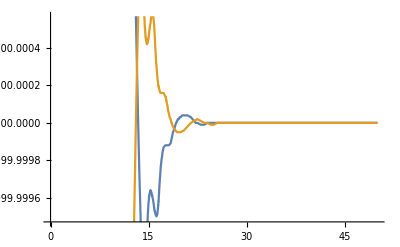

```mathematica
Plot[{sol1[t],sol2[t]},{t,0,50}]
```

## 2.

### a.

DSolve cannot find an analytical solution but NDSolve can approximate a solution given all conditions and can be seen below.

### b.

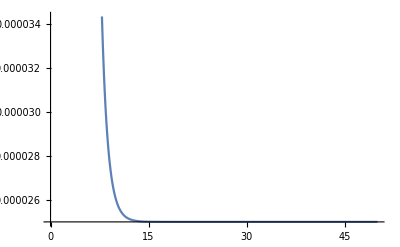

```mathematica
Module[{s,α,n,sol},
s=0.01;
α=1/2;
n=2;
sol[t_]=r[t]/.NDSolve[{r'[t]==s (r[t])^α-n r[t],r[0]==5},r[t],{t,0,50}];
Plot[sol[t],{t,0,50}]]
```

## 3.

### a.

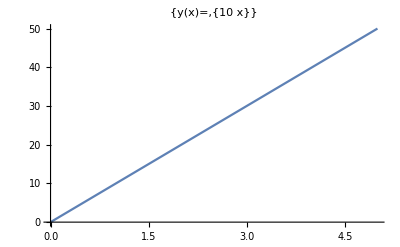

```mathematica
Module[{sol},
sol[x_]=y[x]/.DSolve[{x y'[x]==y[x],y[1]==10},y[x],x];
Plot[sol[x],{x,0,5},PlotLabel->{"y(x)=",sol[x]}]]
```

### b.

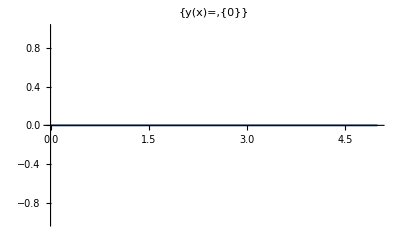

```mathematica
Module[{sol},
sol[x_]=y[x]/.DSolve[{x y'[x]==y[x],y[1]==0},y[x],x];
Plot[sol[x],{x,0,5},PlotLabel->{"y(x)=",sol[x]}]]
```

### c.

```mathematica
Module[{sol},
sol[x_]=y[x]/.DSolve[{x y'[x]==y[x],y[0]==1},y[x],x];
Plot[sol[x],{x,-1,5},PlotLabel->{"y(x)=",sol[x]}]]
```

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

-Graphics-